```mathematica
<<RLBot`
```

```mathematica
SetDirectory[NotebookDirectory[]];
```

```mathematica
datafiles = FileNames["*.ndjson",NotebookDirectory[]];
```

```mathematica
data = ImportNDJSON[datafiles[[7]], {2}][[50;;-1]];
```

```mathematica
Δt = 1.0 / 120.0;
cars = #["car"] & /@ data;
inputs = #["inputs"] & /@ data;
times = #["time"] & /@ data;
actualTimes = #["actual_time"] & /@ data;

x = #["x"]& /@ cars;
v = #["v"]& /@ cars;
ω = #["w"][[3]] & /@ cars;
```

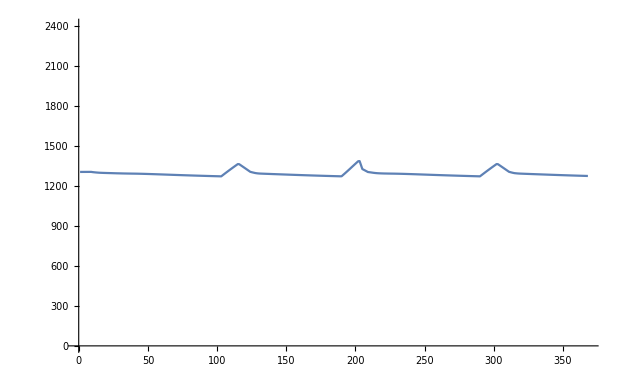

```mathematica
ListLinePlot[Norm /@ v, PlotRange->{0, 2400}]
```

```mathematica
α = Differences[ω]/Differences[times];
steer = #["steer"]& /@ inputs[[1;;-2]];
speeds = Norm /@ v[[1;;-2]];
```

```mathematica
ω
```

{0.00031,0.00021,0.00011,0.00011,0.00011,0.00011,0.00011,354,2.31221,2.31241,2.31271,2.31291,2.31321,2.31341,2.31361}
 |  |  |  |

```mathematica
Transpose[{steer, speeds, ω[[1;;-2]], α}]
```

{{0.,1303.62,0.00031,-0.0120471},{0.,1303.67,0.00021,-0.0119591},363,{1.,1273.98,2.31321,0.0240981},{1.,1273.67,2.31341,0.0238937}}
 |  |  |  |

```mathematica
tuples = {};

Do[
Print[filename];
data = ImportNDJSON[filename, {2}][[50;;-1]];
cars = #["car"] & /@ data;
inputs = #["inputs"] & /@ data;
times = #["time"] & /@ data;

x = #["x"]& /@ cars;
v = #["v"]& /@ cars;
ω = #["w"][[3]] & /@ cars;

α = Differences[ω]/Differences[times];
steer = #["steer"]& /@ inputs[[1;;-2]];
speeds = Norm /@ v[[1;;-2]];

tuples = Join[tuples, Transpose[{steer, speeds, ω[[1;;-2]], α}]]
,
{filename, datafiles}
]
```

C:\Users\sam\Documents\GitHub\RLUtilities\extras\analysis\steering\steering_1000.ndjson

C:\Users\sam\Documents\GitHub\RLUtilities\extras\analysis\steering\steering_1050.ndjson

C:\Users\sam\Documents\GitHub\RLUtilities\extras\analysis\steering\steering_1100.ndjson

C:\Users\sam\Documents\GitHub\RLUtilities\extras\analysis\steering\steering_1150.ndjson

C:\Users\sam\Documents\GitHub\RLUtilities\extras\analysis\steering\steering_1200.ndjson

C:\Users\sam\Documents\GitHub\RLUtilities\extras\analysis\steering\steering_1250.ndjson

C:\Users\sam\Documents\GitHub\RLUtilities\extras\analysis\steering\steering_1300.ndjson

C:\Users\sam\Documents\GitHub\RLUtilities\extras\analysis\steering\steering_1350.ndjson

C:\Users\sam\Documents\GitHub\RLUtilities\extras\analysis\steering\steering_1400.ndjson

C:\Users\sam\Documents\GitHub\RLUtilities\extras\analysis\steering\steering_1450.ndjson

C:\Users\sam\Documents\GitHub\RLUtilities\extras\analysis\steering\steering_1500.ndjson

C:\Users\sam\Documents\GitHub\RLUtilities\extras\analysis\steering\steering_1550.ndjson

C:\Users\sam\Documents\GitHub\RLUtilities\extras\analysis\steering\steering_1600.ndjson

C:\Users\sam\Documents\GitHub\RLUtilities\extras\analysis\steering\steering_1650.ndjson

C:\Users\sam\Documents\GitHub\RLUtilities\extras\analysis\steering\steering_1700.ndjson

C:\Users\sam\Documents\GitHub\RLUtilities\extras\analysis\steering\steering_1750.ndjson

C:\Users\sam\Documents\GitHub\RLUtilities\extras\analysis\steering\steering_1800.ndjson

C:\Users\sam\Documents\GitHub\RLUtilities\extras\analysis\steering\steering_1850.ndjson

C:\Users\sam\Documents\GitHub\RLUtilities\extras\analysis\steering\steering_1900.ndjson

C:\Users\sam\Documents\GitHub\RLUtilities\extras\analysis\steering\steering_1950.ndjson

C:\Users\sam\Documents\GitHub\RLUtilities\extras\analysis\steering\steering_2000.ndjson

C:\Users\sam\Documents\GitHub\RLUtilities\extras\analysis\steering\steering_200.ndjson

C:\Users\sam\Documents\GitHub\RLUtilities\extras\analysis\steering\steering_2050.ndjson

C:\Users\sam\Documents\GitHub\RLUtilities\extras\analysis\steering\steering_2100.ndjson

C:\Users\sam\Documents\GitHub\RLUtilities\extras\analysis\steering\steering_2150.ndjson

C:\Users\sam\Documents\GitHub\RLUtilities\extras\analysis\steering\steering_2200.ndjson

C:\Users\sam\Documents\GitHub\RLUtilities\extras\analysis\steering\steering_2250.ndjson

C:\Users\sam\Documents\GitHub\RLUtilities\extras\analysis\steering\steering_2300.ndjson

C:\Users\sam\Documents\GitHub\RLUtilities\extras\analysis\steering\steering_250.ndjson

C:\Users\sam\Documents\GitHub\RLUtilities\extras\analysis\steering\steering_300.ndjson

C:\Users\sam\Documents\GitHub\RLUtilities\extras\analysis\steering\steering_350.ndjson

C:\Users\sam\Documents\GitHub\RLUtilities\extras\analysis\steering\steering_400.ndjson

C:\Users\sam\Documents\GitHub\RLUtilities\extras\analysis\steering\steering_450.ndjson

C:\Users\sam\Documents\GitHub\RLUtilities\extras\analysis\steering\steering_500.ndjson

C:\Users\sam\Documents\GitHub\RLUtilities\extras\analysis\steering\steering_550.ndjson

C:\Users\sam\Documents\GitHub\RLUtilities\extras\analysis\steering\steering_600.ndjson

C:\Users\sam\Documents\GitHub\RLUtilities\extras\analysis\steering\steering_650.ndjson

C:\Users\sam\Documents\GitHub\RLUtilities\extras\analysis\steering\steering_700.ndjson

C:\Users\sam\Documents\GitHub\RLUtilities\extras\analysis\steering\steering_750.ndjson

C:\Users\sam\Documents\GitHub\RLUtilities\extras\analysis\steering\steering_800.ndjson

C:\Users\sam\Documents\GitHub\RLUtilities\extras\analysis\steering\steering_850.ndjson

C:\Users\sam\Documents\GitHub\RLUtilities\extras\analysis\steering\steering_900.ndjson

C:\Users\sam\Documents\GitHub\RLUtilities\extras\analysis\steering\steering_950.ndjson

```mathematica
filtered = Select[tuples, Abs[#[[3]]] > 0.1 &]
```

{{-1.,1003.84,-0.36141,-32.4548},{-1.,1002.28,-0.63081,-27.781},{-1.,1000.95,-0.86311,-24.0218},15168,{1.,940.686,2.37591,0.},{1.,940.676,2.37591,0.}}
 |  |  |  |

```mathematica
turning = Select[tuples, #[[1]] == -1.0 && Abs[#[[3]]] > 0.1 &&#[[4]] <1&]
```

{{-1.,1003.84,-0.36141,-32.4548},{-1.,1002.28,-0.63081,-27.781},{-1.,1000.95,-0.86311,-24.0218},7434,{-1.,940.697,-2.37591,0.},{-1.,940.686,-2.37591,0.}}
 |  |  |  |

```mathematica
Show[
Plot3D[αFit[0.5, v, ω], {v, 200, 2300}, {ω, -2.5, 2.5}, PlotStyle->Opacity[0.5]],
ListPointPlot3D[filtered[[All, 2;;4]], PlotRange->All]
]
```

-Graphics3D-

```mathematica
ωmax[v_] := steeringCurvature[Abs[v]] Abs[v]
```

```mathematica
Clear[a]
```

```mathematica
Clear[α]
```

```mathematica
αModel[s_, v_, ω_] := c(s ωmax[v] - ω)
```

```mathematica
αFit[s_, v_, ω_] := Evaluate[αModel[s, v, ω] /. fit]
```

```mathematica
Clear[v]
Clear[ω]
```

```mathematica
fit = FindFit[turning, αModel[s, v, ω], c, {s, v, ω}]
```

Experimental`NumericalFunction::dimsl: {v,ω} given in {s,v,ω} should be a list of dimensions for a particular argument.

{c→16.0469}

```mathematica
filtered
```

{{-1.,1003.84,-0.36141,-32.4548},{-1.,1002.28,-0.63081,-27.781},{-1.,1000.95,-0.86311,-24.0218},15168,{1.,940.686,2.37591,0.},{1.,940.676,2.37591,0.}}
 |  |  |  |

```mathematica
DeleteDuplicatesBy
```